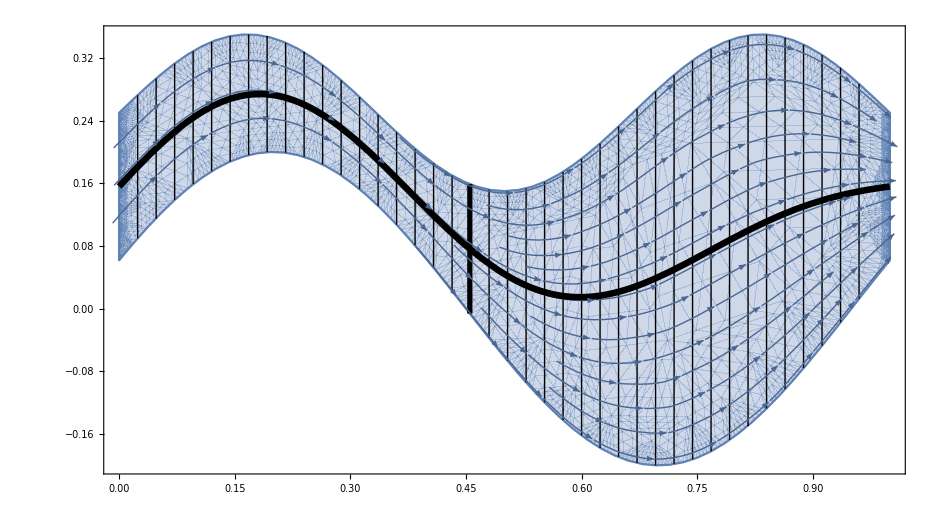

```mathematica
(* Channel creation *)
y1=Cos[2Pi (x-.2)]/5;
y2=1/4+Sin[3Pi x]/10;
c=(y1+y2)/2;
w=y2-y1;
p={x,c+v w};
channel=ParametricRegion[p,{{x,0,1},{v,-1/2,1/2}}];

(* Generating Vector field *)
U=Simplify[D[p,x]/.v->(y-c)/w];

(* Graphics *)
UG=StreamPlot[U,{x,y}∈channel];
channelG=RegionPlot[channel,AspectRatio->Automatic];
midLineG=ParametricPlot[{x,c},{x,0,1},PlotStyle->Directive[Black,Thickness[.005]]];
sectionG=ParametricPlot[p/.x->.455,{v,-1/2,1/2},PlotStyle->Directive[Black,Thickness[.004]]];
levelsG=ContourPlot[x,{x,0,1},{y,-1,1},ContourShading->None,Contours->40,RegionFunction->Function[{x,y},Evaluate[y1<y<y2]]];
Show[channelG,levelsG,sectionG,UG,midLineG]
```

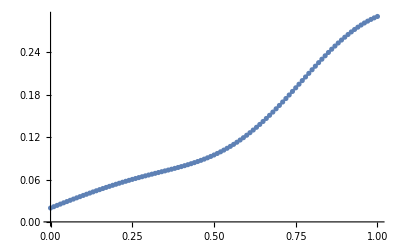

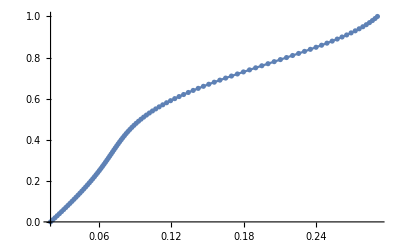

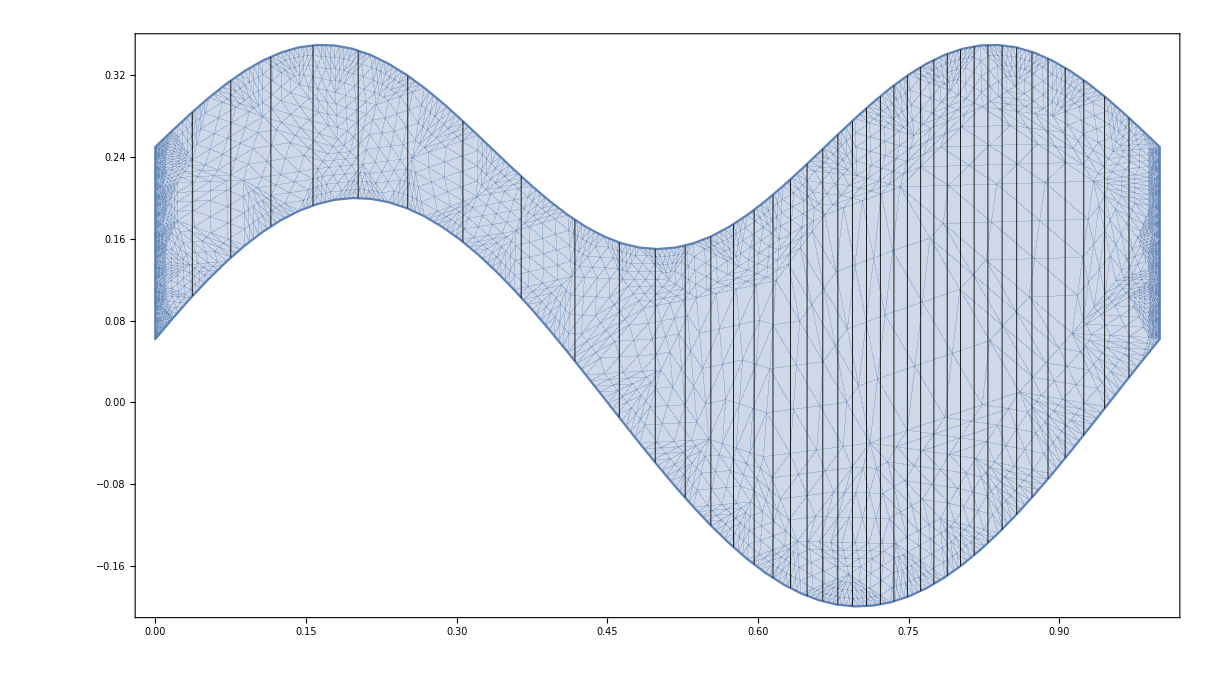

```mathematica
(* Area stuff *)
ν=Simplify[Integrate[w,x]];
xStep = .01;
νs=Table[{xVal,ν/.x->xVal},{xVal,0,1,xStep}];
us=Table[{ν/.x->xVal,xVal},{xVal,0,1,xStep}];
Show[Plot[ν,{x,0,1}],ListPlot[νs]]
uf=Interpolation[us];
vMin=Min[Transpose[νs][[2]]];
vMax=Max[Transpose[νs][[2]]];
Show[Plot[uf[v],{v,vMin,vMax}],ListPlot[us]]
vCount=40;
vStep = (vMax-vMin)/vCount;
regνs=Table[v,{v,vMin,vMax,vStep}];
sus = uf/@regνs;
lG=ContourPlot[x,{x,0,1},{y,-1,1},ContourShading->None,Contours->sus,RegionFunction->Function[{x,y},Evaluate[y1<y<y2]],ContourStyle->Directive[Thickness[.0005]]];
Show[channelG,lG]
```

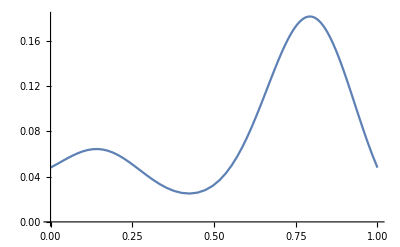

```mathematica
wf[xv_]=w/.x->xv;
ListPlot[Transpose[{sus,(wf/@sus)^2}],Joined->True]
```